# Some details from the Exop GW strain calcultions.

20170228 weg, start this notebook to look at any analytic calculations for the rise and fall of the g(n,e) vs n.  Want the
  frequency “bandwidth,” the significant harmonics in the wave.

## g(n,e) Peters and Mathews

```mathematica
(*myDir = "/scratch/gabella/Documents/astro/exop/";*)
myDir = "/home/gabella/Documents/astro/exop/";
```

```mathematica
jj = BesselJ
```

BesselJ

```mathematica
ggPM[n_,e_]:= n^4/32( (jj[n-2,n e]-2 e jj[n-1,n e]+2/n jj[n, n e]+2 e jj[n+1, n e]-jj[n+2, n e])^2+
(1-e^2)(jj[n-2,n e]-2 jj[n, n e]+jj[n+2, n e])^2 +4/(3 n^2)jj[n, n e]^2 )
```

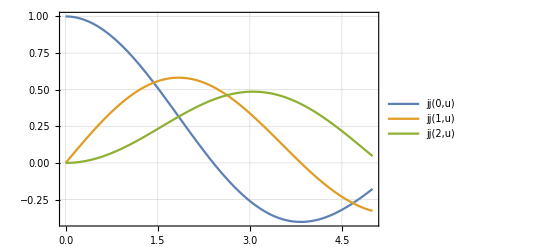

```mathematica
Plot[{jj[0,u],jj[1,u],jj[2,u]},{u,0,5}, PlotTheme->"Detailed"]
```

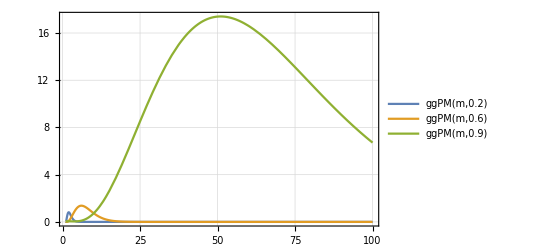

```mathematica
Plot[{ggPM[m,0.2], ggPM[m,0.6], ggPM[m, 0.9]},{m, 1, 100}, PlotTheme->"Detailed"]
```

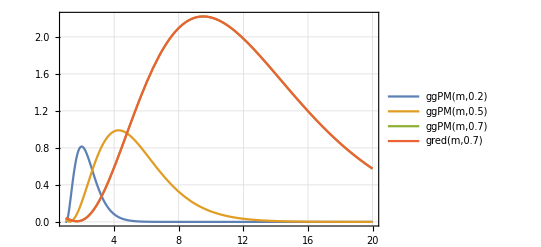

```mathematica
Plot[{ggPM[m,0.2], ggPM[m,0.5], ggPM[m, 0.7]},{m, 1, 20}, PlotTheme->"Detailed"]
```

```mathematica
exp1 = Expand[ggPM[n,e]*32/n^4*(3 e^4 n^2)/16]//FullSimplify
```

3 e^2 (-1+e^2) (-1+(-1+e^2) n^2) BesselJ[-1+n,e n]^2-3 e (-1+e^2) (-2+n (-2 (2+n)+e^2 (3+2 n))) BesselJ[-1+n,e n] BesselJ[n,e n]+(-3 e^6 n^2+6 (1+n)^2-3 e^2 (1+n) (2+5 n)+e^4 (1+3 n (3+4 n))) BesselJ[n,e n]^2

```mathematica
gred[n_,e_]:=n^2/(6 e^4)(
3 e^2 (-1+e^2) (-1+(-1+e^2) n^2) BesselJ[-1+n,e n]^2-3 e (-1+e^2) (-2+n (-2 (2+n)+e^2 (3+2 n))) BesselJ[-1+n,e n] BesselJ[n,e n]+(-3 e^6 n^2+6 (1+n)^2-3 e^2 (1+n) (2+5 n)+e^4 (1+3 n (3+4 n))) BesselJ[n,e n]^2   )
```

```mathematica
poly1 = exp1[[1]]
```

3 e^2 (-1+e^2) (-1+(-1+e^2) n^2) BesselJ[-1+n,e n]^2

```mathematica
poly2 = exp1[[2]]
```

-3 e (-1+e^2) (-2+n (-2 (2+n)+e^2 (3+2 n))) BesselJ[-1+n,e n] BesselJ[n,e n]

```mathematica
poly3 = exp1[[3]]
```

(-3 e^6 n^2+6 (1+n)^2-3 e^2 (1+n) (2+5 n)+e^4 (1+3 n (3+4 n))) BesselJ[n,e n]^2

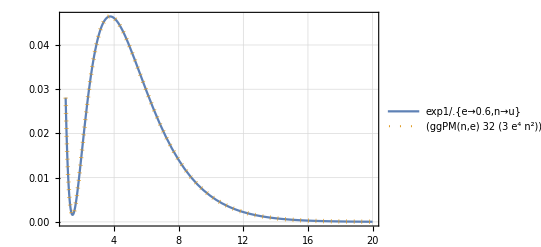

```mathematica
Plot[{exp1/.{e->0.6,n->u}, (ggPM[n,e]*32/n^4*(3 e^4 n^2)/16)/.{e->0.6,n->u}},{u,1,20},
PlotStyle->{{Joined},{Dotted, Thickness[0.008]}},PlotTheme->"Detailed"]
```

```mathematica
(*Factor[exp1]*)
```

```mathematica
(*FactorTerms[exp1]*)
```

```mathematica
(*Export[myDir<>"test.tex", exp1, "TeX"]*)
```

/home/gabella/Documents/astro/exop/test.tex

```mathematica
exp1
```

3 e^2 (-1+e^2) (-1+(-1+e^2) n^2) BesselJ[-1+n,e n]^2-3 e (-1+e^2) (-2+n (-2 (2+n)+e^2 (3+2 n))) BesselJ[-1+n,e n] BesselJ[n,e n]+(-3 e^6 n^2+6 (1+n)^2-3 e^2 (1+n) (2+5 n)+e^4 (1+3 n (3+4 n))) BesselJ[n,e n]^2

```mathematica
exp1first = exp1 /. {BesselJ[n,e n]->0, BesselJ[-1+n,e n]->1}
```

3 e^2 (-1+e^2) (-1+(-1+e^2) n^2)

```mathematica
exp1second = exp1 /. {BesselJ[n,e n]->0, BesselJ[-1+n,e n]->0,  BesselJ[-1+n,e n] BesselJ[n,e n]->1}
```

-3 e (-1+e^2) (-2+n (-2 (2+n)+e^2 (3+2 n)))

```mathematica
exp1third = exp1/.{BesselJ[n,e n]->1, BesselJ[-1+n,e n]->0,  BesselJ[-1+n,e n] BesselJ[n,e n]->0}
```

-3 e^6 n^2+6 (1+n)^2-3 e^2 (1+n) (2+5 n)+e^4 (1+3 n (3+4 n))

```mathematica
exp1third //FullSimplify //Factor
```

6-6 e^2+e^4+12 n-21 e^2 n+9 e^4 n+6 n^2-15 e^2 n^2+12 e^4 n^2-3 e^6 n^2

```mathematica
Factor[6 -6 e^2+e^4+12n+6 n^2]
```

6-6 e^2+e^4+12 n+6 n^2

```mathematica
FactorTerms[6 -6 e^2+e^4+12n+6 n^2]
```

6-6 e^2+e^4+12 n+6 n^2

```mathematica
aa=(3-e^2)^2+6(n+1)^2-9;
Expand[aa]
```

6-6 e^2+e^4+12 n+6 n^2

```mathematica
exp13b = (exp1third-( (3-e^2)^2+6(n+1)^2 -9))/(3n e^2)/. e->√u//Expand//Expand
```

-7-5 n+3 u+4 n u-n u^2

```mathematica
Factor[exp13b]
```

-7-5 n+3 u+4 n u-n u^2

```mathematica
bb = (A u + B n u + C n)^2//Expand
```

C^2 n^2+2 A C n u+2 B C n^2 u+A^2 u^2+2 A B n u^2+B^2 n^2 u^2

## Asymptotics from A&S page 365, 9.3.1.

```mathematica
asyjj[n_,z_]:=((E*z)/(2n))^n 1/(√(2π n))
asyyy[n_,z_]:=-((E*z)/(2n))^-n √(2/πn)
```

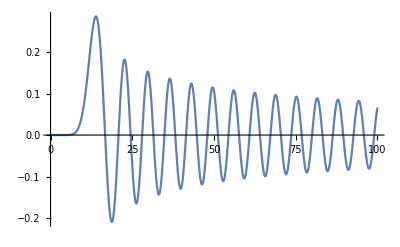

```mathematica
Plot[jj[12,u],{u,0,100}]
```

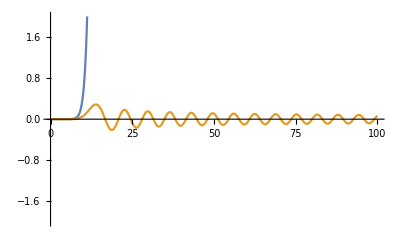

```mathematica
Plot[{asyjj[12,u],jj[12,u]}, {u, 0, 100},
PlotRange->{{-2,2}}]
```

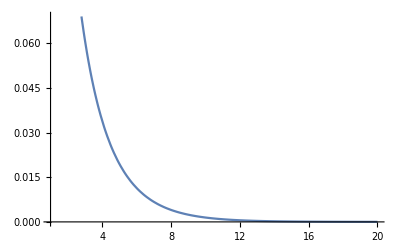

```mathematica
Plot[jj[n,n*0.5],{n, 1, 20}]
```

```mathematica
plist = Table[jj[i,i*e],{i,3,30,4}]
```

{BesselJ[3,3 e],BesselJ[7,7 e],BesselJ[11,11 e],BesselJ[15,15 e],BesselJ[19,19 e],BesselJ[23,23 e],BesselJ[27,27 e]}

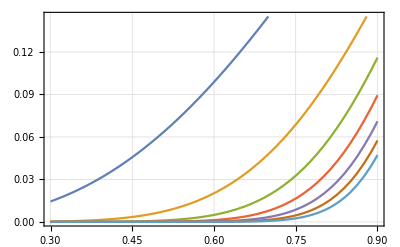

```mathematica
Plot[plist,{e,0.3, 0.9}, PlotTheme->"Detailed"]
```

```mathematica
Plot3D[jj[n,n e], {n, 1, 20},{e, 0, 0.9}]
```

-Graphics3D-

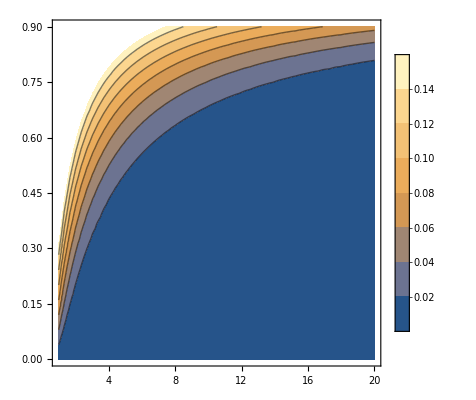

```mathematica
ContourPlot[jj[n,n e], {n, 1, 20},{e, 0, 0.9}, PlotTheme->"Detailed"]
```

```mathematica
gred[n, e]
```

1/(6 e^4)n^2 (3 e^2 (-1+e^2) (-1+(-1+e^2) n^2) BesselJ[-1+n,e n]^2-3 e (-1+e^2) (-2+n (-2 (2+n)+e^2 (3+2 n))) BesselJ[-1+n,e n] BesselJ[n,e n]+(-3 e^6 n^2+6 (1+n)^2-3 e^2 (1+n) (2+5 n)+e^4 (1+3 n (3+4 n))) BesselJ[n,e n]^2)

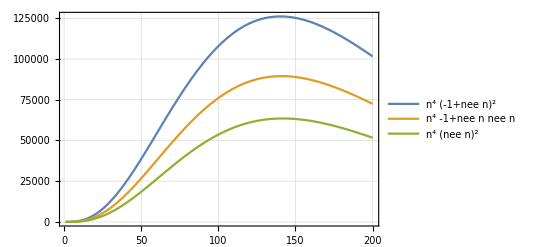
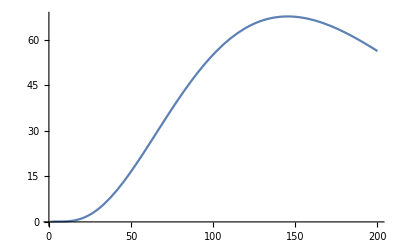

```mathematica
Block[{ee=0.95},
{Plot[{n^4 BesselJ[-1+n,ee n]^2, n^4 BesselJ[-1+n,ee n] BesselJ[n,ee n],n^4 BesselJ[n,ee n]^2},{n, 1, 200}, PlotTheme->"Detailed"],
Plot[gred[n, ee], {n, 1, 200} ]  }    ]
```

```mathematica
aa[n_,e_]:=3 e^2 (-1+e^2) (-1+(-1+e^2) n^2)  (** looks like n^2 for large enough n vs e **)
bb[n_, e_]:= 3 e (-1+e^2) (-2+n (-2 (2+n)+e^2 (3+2 n)))
cc[n_, e_]:= (-3 e^6 n^2+6 (1+n)^2-3 e^2 (1+n) (2+5 n)+e^4 (1+3 n (3+4 n)))
```

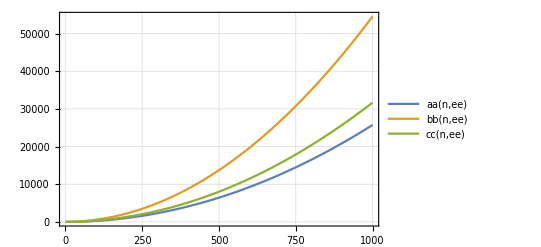

```mathematica
Block[{ee=0.95},
Plot[{aa[n,ee], bb[n, ee], cc[n, ee]},{n, 1, 1000}, PlotTheme->"Detailed"]
]
```

```mathematica
Expand[aa[1/u,e],u] (* small u is large n *)
```

-3 e^2 (-1+e^2)+(3 e^2 (-1+e^2)^2)/u^2

```mathematica
Expand[bb[1/u,e],u]
```

-6 e (-1+e^2)-(6 e (-1+e^2))/u^2+(6 e^3 (-1+e^2))/u^2-(12 e (-1+e^2))/u+(9 e^3 (-1+e^2))/u

```mathematica
Expand[cc[1/u,e],u]
```

6-6 e^2+e^4+6/u^2-(15 e^2)/u^2+(12 e^4)/u^2-(3 e^6)/u^2+12/u-(21 e^2)/u+(9 e^4)/u

```mathematica
Expand[jj[1/u, 1/u e], u]
```

BesselJ[1/u,e/u]

```mathematica
Expand[gred[1/u,e],u]//FullSimplify
```

1/(6 e^4 u^4)(3 e^2 (-1+e^2) (-1+e^2-u^2) BesselJ[-1+1/u,e/u]^2-3 e (-1+e^2) (-2 (1+u)^2+e^2 (2+3 u)) BesselJ[-1+1/u,e/u] BesselJ[1/u,e/u]+(-3 e^6+6 (1+u)^2-3 e^2 (1+u) (5+2 u)+e^4 (12+u (9+u))) BesselJ[1/u,e/u]^2)

```mathematica
Series[gred[1/u,e],{u,0,3}]
```

BesselJ[-1+1/u,e/u]^2 ((1-2 e^2+e^4)/(2 e^2 u^4)+(1-e^2)/(2 e^2 u^2)+O[u]^2)+BesselJ[-1+1/u,e/u] BesselJ[1/u,e/u] (-(e-2 e^3+e^5)/(e^4 u^4)+(-4+7 e^2-3 e^4)/(2 e^3 u^3)+(-1+e^2)/(e^3 u^2)+O[u]^2)+BesselJ[1/u,e/u]^2 ((6-15 e^2+12 e^4-3 e^6)/(6 e^4 u^4)+(12-21 e^2+9 e^4)/(6 e^4 u^3)+(6-6 e^2+e^4)/(6 e^4 u^2)+O[u]^2)

```mathematica
gred[1,e]//FullSimplify
```

1/(6 e^4)(3 e^2 (2-3 e^2+e^4) BesselJ[0,e]^2-3 e (8-13 e^2+5 e^4) BesselJ[0,e] BesselJ[1,e]+(4-3 e^2) (6-6 e^2+e^4) BesselJ[1,e]^2)

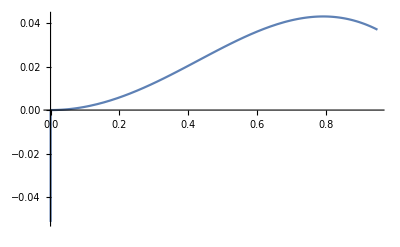

```mathematica
Plot[ gred[1,e], {e, 0, 0.95}]
```

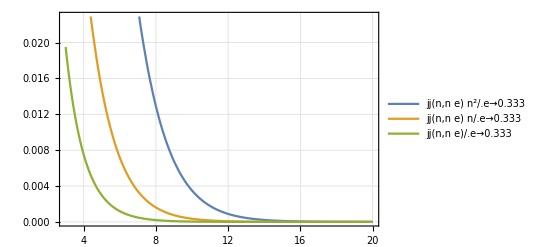

```mathematica
Plot[ {jj[n, n e]*n^2/.e->0.333,jj[n, n e ]*n/.e->0.333, jj[n, n e]/.e->0.333}, {n, 3,20}, PlotTheme->"Detailed"]
```

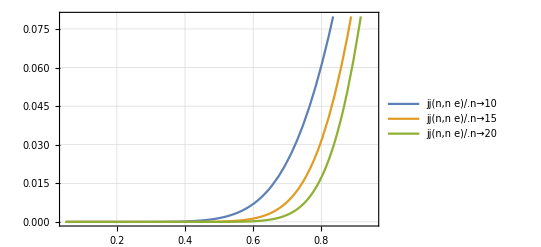

```mathematica
Plot[ {jj[n, n e]/.n->10,jj[n, n e ]/.n->15, jj[n, n e]/.n->20}, {e, 0.05,0.95}, PlotTheme->"Detailed"]
```

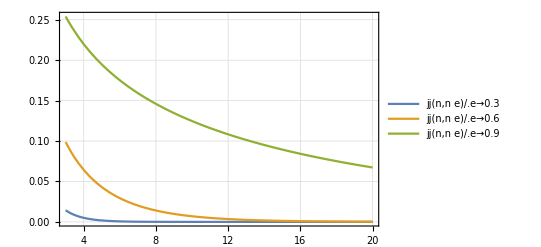

```mathematica
Plot[ {jj[n, n e]/.e->0.3,jj[n, n e ]/.e->0.6, jj[n, n e]/.e->0.9}, {n, 3,20}, PlotTheme->"Detailed"]
```

```mathematica
bessDE = z^2 y[z]''+zy[z]'+(z^2-n^2)y==0
```

y (-n^2+z^2)+zy[z]'+z^2 y[z]''==0

```mathematica
bessDE/.{z->x, y[z]->BesselJ[n,x]}
```

(-n^2+x^2) y+zy[x]'+x^2 BesselJ[n,x]''==0

```mathematica
ii = BesselI
kk = BesselK
```

BesselI

BesselK

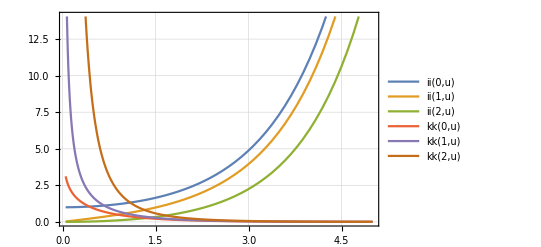

```mathematica
Plot[{ii[0,u],ii[1,u],ii[2,u],kk[0,u],kk[1,u],kk[2,u]},{u,0.05, 5},PlotTheme->"Detailed"]
```

```mathematica
Plot[{kk[0,u],kk[1,u],kk[2,u]},{u,0.05, 5},PlotTheme->"Detailed"]
```

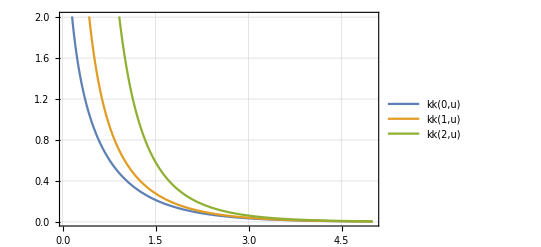

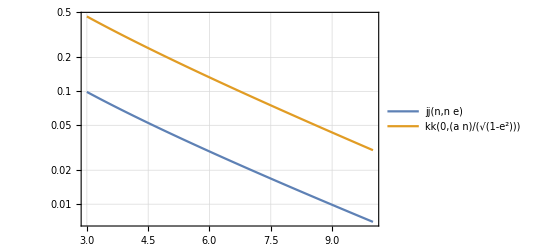

```mathematica
Block[{e=0.6,a=0.25},
LogPlot[{jj[n,n e], kk[0,a n/(√(1-e^2))]},{n,3,10},PlotTheme->"Detailed"]
]
```

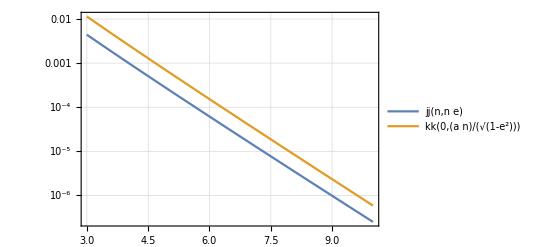

```mathematica
Block[{e=0.2,a=1.3},
LogPlot[{jj[n,n e], kk[0,a n/(√(1-e^2))]},{n,3,10},PlotTheme->"Detailed"]
]
```

```mathematica
(√(1-#^2)&)/@{0.2, 0.6, 0.8}
```

{0.979796,0.8,0.6}

```mathematica
(1-#^2&)/@{0.2, 0.6, 0.8}
```

{0.96,0.64,0.36}

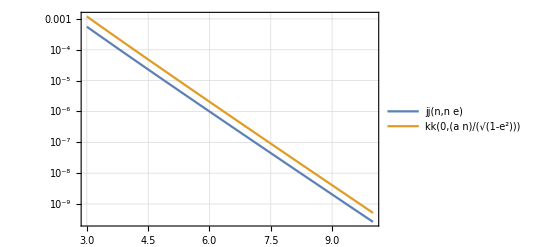

```mathematica
Block[{e=0.1,a=2},
LogPlot[{jj[n,n e], kk[0,a n/(√(1-e^2))]},{n,3,10},PlotTheme->"Detailed"]
]
```

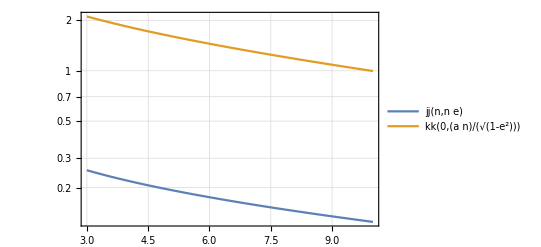

```mathematica
Block[{e=0.9,a=0.02},
LogPlot[{jj[n,n e], kk[0,a n/(√(1-e^2))]},{n,3,10},PlotTheme->"Detailed"]
]
```

```mathematica
data = {{0.1, 2.0},{0.2, 1.3},{0.6, 0.25},{0.9, 0.02}}; (* {e,a}, eccentricity and fudge factor *)
```

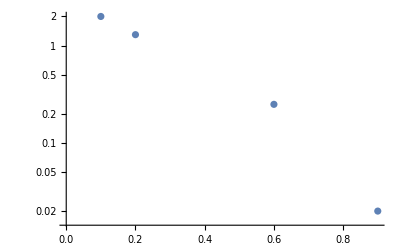

```mathematica
aplot = ListLogPlot[data]
```

```mathematica
afit = Fit[data,{1,u,u^2}, u]
```

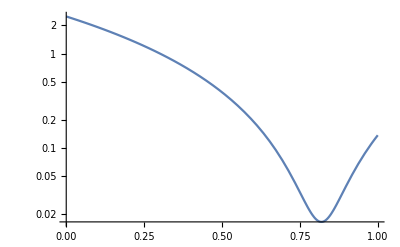

```mathematica
bplot = LogPlot[afit, {u, 0, 1}]
```

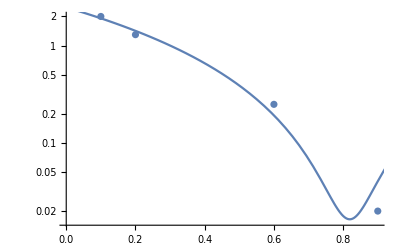

```mathematica
Show[{aplot, bplot}]
```

```mathematica
{ee, aa} = Transpose[data];
newdata = Transpose[{ee, Log[aa]}];
bfit = Fit[newdata, {1,w},w]
```

1.41295-5.55255 w

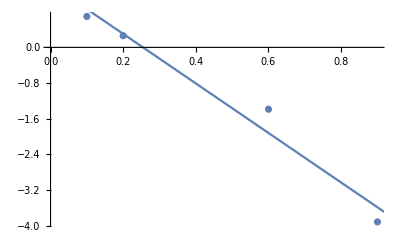

```mathematica
cplot = ListPlot[newdata];
dplot = Plot[bfit,{w,0.05, 0.95}];
Show[{cplot, dplot}]
```

```mathematica
Exp[1.41-5.55 x]//FullSimplify
```

4.09596 ⅇ^(-5.55 x)

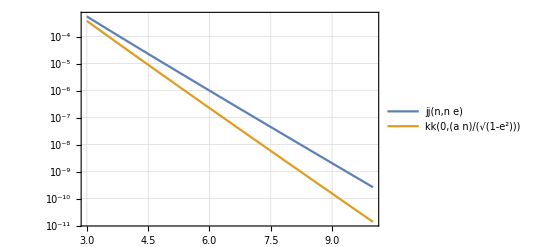

```mathematica
Block[{e=0.1, a},
a = 4.1 Exp[-5.55*e];
LogPlot[{jj[n,n e], kk[0,a n/(√(1-e^2))]},{n,3,10},PlotTheme->"Detailed"]
]
```

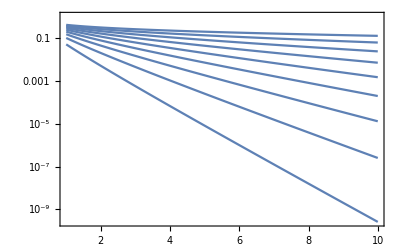

```mathematica
Module[{emin=0.1, emax=0.9,n, e},
toplot = Table[jj[n, n e],{e,emin, emax, 0.1}];
LogPlot[toplot,{n,1,10},PlotTheme->"Detailed"]
]
```

```mathematica
Table[jj[n, n e],{e,0.1,0.9, 0.1}]
```

{BesselJ[n,0.1 n],BesselJ[n,0.2 n],BesselJ[n,0.3 n],BesselJ[n,0.4 n],BesselJ[n,0.5 n],BesselJ[n,0.6 n],BesselJ[n,0.7 n],BesselJ[n,0.8 n],BesselJ[n,0.9 n]}

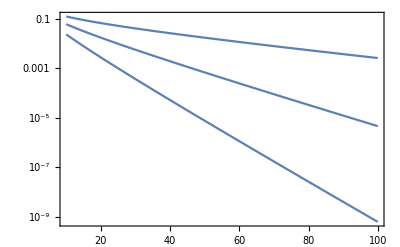

```mathematica
Module[{emin=0.7, emax=0.9,n, e},
toplot = Table[jj[n, n e],{e,emin, emax, 0.1}];
LogPlot[toplot,{n,10,100},PlotTheme->"Detailed"]
]
```

Find the slope of log( j(n,n e) ) when j(n, n e) is small-ish, less than 0.1 to 1e-big.  Do it over many orders of magnitude.
Awkward because of the index nature of n in J[n, n e], so do a data fit selecting out values from 0.1 to 1e-6.

```mathematica
logslope=Module[{e=0.9, emin=0.05, emax = 0.95, data, ystart= 0.1, yend = 10^-6,nmin, nmax,a, b, datanew, xdatanew, ydatanew, datalog, w, aslope, alist={}},
For[e=emin, e≤emax, e+=0.05,

data = Table[{n, jj[n, n e]},{n, 1, 100}];
For[ii=1, ii<=Length[data], ii++,
If[data[[ii,2]]<ystart, nmin=ii; Break[];  ] ];
For[ii=1, ii<=Length[data], ii++,
If[data[[ii,2]]<yend, nmax=ii;Break [], nmax=100  ]  ];
(*Print["Ecc ", e, " nmin ", nmin, " nmax ", nmax];*)
datanew = data[[Range[nmin, nmax] ]];
{xdatanew, ydatanew} = Transpose[ datanew ];
datalog = Transpose[ {xdatanew, Log[ydatanew] } ];
aslope = Fit[datalog, {1,w},w][[2,1]];
(*Print[aslope];*)
alist~AppendTo~{e, aslope};
(*Print["Ecc ",e," nmin ", nmin, " nmax ", nmax]*)

];(* end For e *)
alist
]
```

{{0.05,-2.87012},{0.1,-2.15752},{0.15,-1.72508},{0.2,-1.43062},{0.25,-1.18071},{0.3,-0.995477},{0.35,-0.841855},{0.4,-0.709051},{0.45,-0.593664},{0.5,-0.491142},{0.55,-0.404696},{0.6,-0.328101},{0.65,-0.259192},{0.7,-0.199603},{0.75,-0.147666},{0.8,-0.104432},{0.85,-0.0695641},{0.9,-0.0407826},{0.95,-0.0186674}}

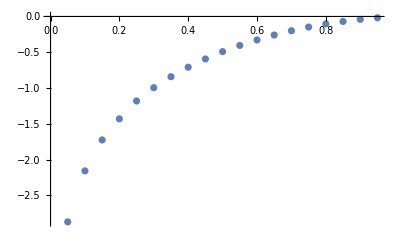

a ⅇ^(b w)

{a→-3.36166,b→-4.0733}

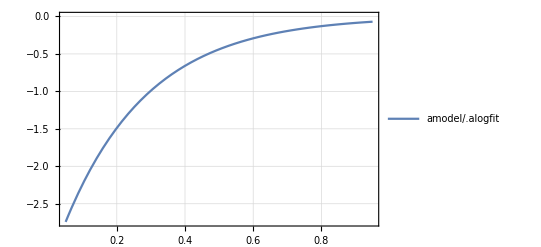

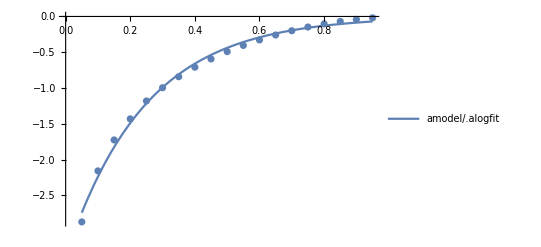

```mathematica
aplot=ListPlot[logslope]
amodel = a Exp[b w]
alogfit = FindFit[logslope, amodel, {a,b},w]
bplot = Plot[amodel/.alogfit, {w, 0.05, 0.95}, PlotTheme->"Detailed"]
Show[{aplot, bplot}]
```

```mathematica
{Exp[-3.362],Exp[-4.0733],1/Exp[-3.362],1/Exp[-4.0733]}
```

{0.0346659,0.0170211,28.8468,58.7505}

-Graphics-

a+b w+c w^2

{a→-2.81564,b→6.93874,c→-4.37067}

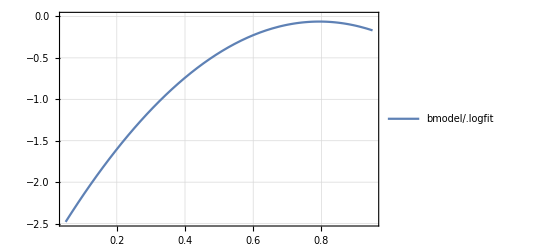

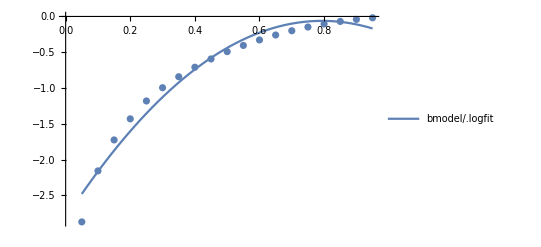

```mathematica
aplot=ListPlot[logslope]
bmodel = a+b w+c w^2
logfit = FindFit[logslope, bmodel, {{a,-3.0},b,c},w]
bplot = Plot[bmodel/.logfit, {w, 0.05, 0.95}, PlotTheme->"Detailed"]
Show[{aplot, bplot}]
```

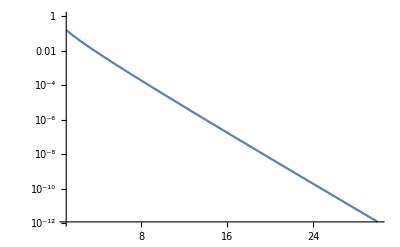

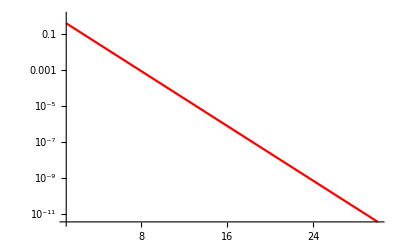

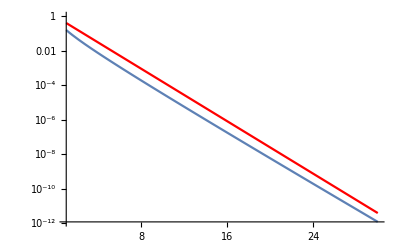

```mathematica
e=0.33;
aplot=LogPlot[jj[n,n e],{n, 1, 30}]
aslope = amodel/.alogfit;
Clear[afcn];
afcn[n_,e_]:= Exp[(aslope/.w->e) n]
bplot = LogPlot[ afcn[n,e], {n, 1, 30}, PlotStyle->RGBColor[1,0,0] ]
Show[{aplot,bplot}]
```

```mathematica
Range[4,6]
```

{4,5,6}

```mathematica
Range[4,6]~AppendTo~99
```

Set::write: Tag Range in Range[4,6] is Protected.

{4,5,6,99}

```mathematica
alist = {5,6,7,3,4}
alist[[{1,4}]]
```

{5,6,7,3,4}

{5,3}

```mathematica
Module[{e =0.05},
data = Table[{n, jj[n, n e]},{n, 1, 100}];
data[[Length[data] ]]
(*ListPlot[data]*)
]
```

{100,6.26779×10^-119}

```mathematica
Module[{yth, e, asol, afcn},
e=0.8;
yth=0.1;
afcn[nn_]:=jj[n, n e];
asol=NSolve[ afcn[n]-yth==0, n, Reals]
]
```

NSolve[-0.1+BesselJ[n,0.8 n]==0,n,Reals]

```mathematica
NSolve[BesselJ[n
```